```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../Models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,WFCorrections,SelfEnergyCTs}];
```

```mathematica
FR$ClassesTranslation
```

FR$ClassesTranslation

```mathematica
tops = CreateTopologies[1, 2->4,  ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,WFCorrections}];
```

## Quark initiated process

### Remove diagrams which are identically zero due to color conservation and only of order yDM gs^2

```mathematica
processQQTT =  { F[7],-F[7]} -> {F[9], -F[9], F[9], -F[9]};
allDiags = InsertFields[tops,processQQTT, InsertionLevel-> {Particles},ExcludeParticles->{F[12],V[1],V[2],V[3]},LastSelections->{S[4]}];
(* Set Truncated->True to remove external fields  *)
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},List->True,TransversePolarizationVectors->{p1,p2},DropSumOver->False,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings,ChangeDimension->D];
nonZero={};
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	If[M=={0},Continue[]];
	If[SeriesCoefficient[DiracSimplify[M/.GS-> √(4 Pi aS)],{yDM,0,2},{aS,0,1}]=={0},Continue[]];
	AppendTo[nonZero,n];
];
goodDiags=DiagramExtract[allDiags,nonZero];
Paint[goodDiags,ColumnsXRows->{1,1},ImageSize->{ 250,250},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

generic model {Lorentz} initialized

classes model {../../Models/SMS-stop-FA/SMS-stop-FA} initialized

in total: 214 Particles insertions

in total: 214 Particles amplitudes

## Gluon initiated process

### Remove diagrams which are identically zero due to color conservation and only of order yDM gs^2

in total: 17 Particles insertions

in total: 17 Particles amplitudes

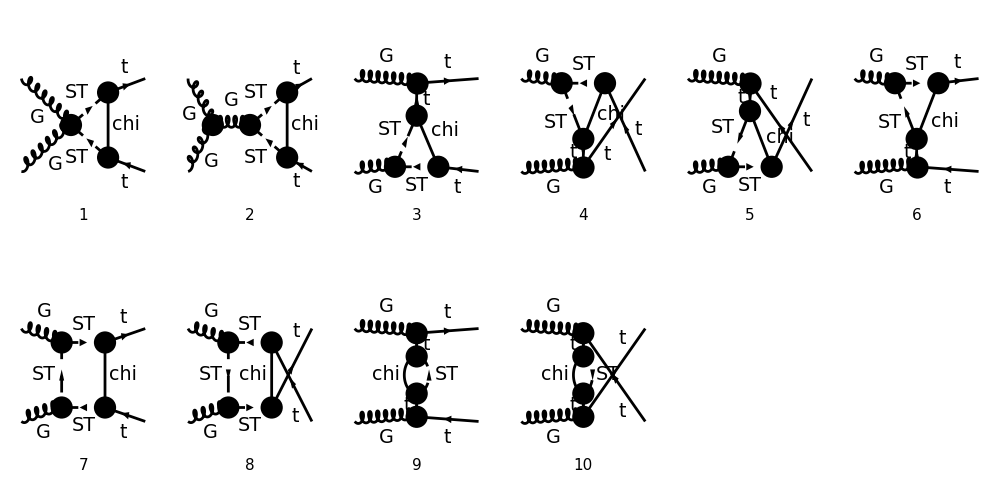

```mathematica
processGGTT =  { V[4],V[4]} -> {F[9], -F[9], F[9], -F[9]};
allDiags = InsertFields[tops,processGGTT, InsertionLevel-> {Particles},ExcludeParticles->{F[12],V[1],V[2],V[3]},LastSelections->{S[4]}];
(* Set Truncated->True to remove external fields  *)
amp=FCFAConvert[CreateFeynAmp[allDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT, GS-> √(4 Pi aS)},IncomingMomenta->{p1,p2},OutgoingMomenta->{k1,k2},LoopMomenta->{q},List->True,TransversePolarizationVectors->{p1,p2},DropSumOver->False,SMP->True,List->False,LorentzIndexNames-> {μ,ν},Contract->False,UndoChiralSplittings->True,FinalSubstitutions-> M$FACouplings,ChangeDimension->D];
nonZero={};
For[n=1,n≤Length[amp],++n,
	M = Take[amp,{n}];
	M = SUNSimplify[M];
	If[M=={0},Continue[]];
	If[SeriesCoefficient[DiracSimplify[M/.GS-> √(4 Pi aS)],{yDM,0,2},{aS,0,1}]=={0},Continue[]];
	AppendTo[nonZero,n];
];
goodDiags=DiagramExtract[allDiags,nonZero];
Paint[goodDiags,ColumnsXRows->{IntegerPart[Length[nonZero]/2]+1,2},ImageSize->{ 1000,500},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```